```mathematica
Directory[]
```

/Users/penn

```mathematica
SetDirectory["/Users/penn/Documents"]
```

/Users/penn/Documents

```mathematica
data=Import["xyh.txt","Table"]
```

{{1.05117108181×10^6,3.19993775403×10^6,26.3685},{1.05126108181×10^6,3.20002775403×10^6,25.1082},{1.05126108181×10^6,3.19993775403×10^6,25.8275},50593,{1.13271108181×10^6,3.11479775403×10^6,13.7533},{1.13280108181×10^6,3.11506775403×10^6,13.6504},{1.13280108181×10^6,3.11497775403×10^6,13.6916}}
 |  |  |  |

```mathematica
z=Map[#[[3]]&,data]
```

{26.3685,25.1082,25.8275,23.1285,23.8478,24.5671,21.8682,22.5875,20.6078,21.3271,20.7815,20.9326,21.0837,21.6459,21.797,22.6614,23.4169,23.6768,24.2812,24.4324,24.6923,50557,13.7517,13.5662,13.7726,13.5871,13.7935,13.608,13.7731,13.8144,13.5876,13.6289,13.7527,13.794,13.6085,13.7324,13.7737,13.6294,13.6707,13.712,13.7533,13.6504,13.6916}
 |  |  |  |

```mathematica
perimeter=Map[{#[[1]],#[[2]]}&,data];
```

```mathematica
perimeter
```

{{1.05117108181×10^6,3.19993775403×10^6},{1.05126108181×10^6,3.20002775403×10^6},{1.05126108181×10^6,3.19993775403×10^6},{1.05135108181×10^6,3.20020775403×10^6},50592,{1.13271108181×10^6,3.11479775403×10^6},{1.13280108181×10^6,3.11506775403×10^6},{1.13280108181×10^6,3.11497775403×10^6}}
 |  |  |  |

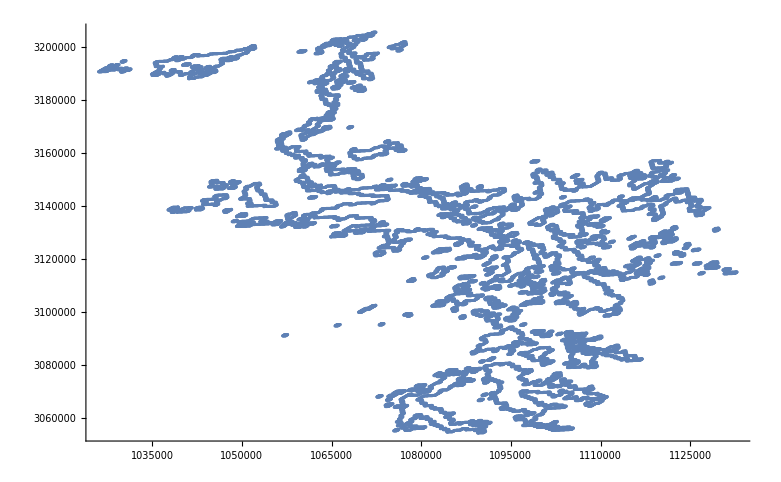

```mathematica
ListPlot[perimeter]
```